```mathematica
Clear["Global`*"]
```

```mathematica
<<"CFMLab`BlackScholes`"

<<"CFMLab`NumericalBlackScholes`"
<<"CFMLab`StockStat`"
```

```mathematica
SetDirectory[ToFileName[{$TopDirectory,"AddOns","Applications","CFMLab","MarketData"}]]
```

C:\Program Files\Wolfram Research\Mathematica\8.0\AddOns\Applications\CFMLab\MarketData

```mathematica
FileNames["*data*"]
```

{option data0507.txt,option data0508.txt,option data.txt,OptionMetricsData1.txt,OptionMetricsData2.txt,stock data.txt}

```mathematica
InputData=OpenRead["stock data.txt"]
```

InputStream[stock data.txt,30]

```mathematica
Tickers=Table[Read[InputData,Word],{1}]
```

{MSFT}

```mathematica
AllData=Table[Read[InputData,Word],{1518}];
```

```mathematica
Take[AllData,1518];
```

```mathematica
Close[InputData]
```

stock data.txt

```mathematica
TradingDates=Select[AllData,StringPosition[#,"/"]≠{}&];
```

```mathematica
x=Position[AllData,#]&/@TradingDates;
Take[AllData,{x[[-1,1,1]]}]
```

{5/8/13}

```mathematica
Take[AllData,{x[[-1,1,1]],x[[-1,1,1]]+1}]
```

{5/8/13,32.99}

```mathematica
AllData2=Module[{x,y},x=Position[AllData,#]&/@TradingDates;
y=Take[AllData,#-{0,1}]&/@Partition[Flatten[x],2,1];Append[y,Take[AllData,{x[[-1,1,1]],x[[-1,1,1]]+1}]]];
```

```mathematica
TextPriceData["MSFT"]=AllData2;
```

```mathematica
PriceData[Ticker_]:=Function[X,{Module[{xx,yy},xx=Partition[Append[Prepend[#[[1]]&/@StringPosition[#,"/"],0],StringLength[#]+1],2,1];
yy=ToExpression[Function[y,StringTake[#,y+{1,-1}]]/@xx];{#[[3]]+2000,#[[1]],#[[2]],16,0,0}&[yy]]&[X[[1]]],ToExpression[X[[2]]]}]/@TextPriceData[Ticker]
```

```mathematica
TextPriceData["MSFT"][[1]]
```

{5/4/10,30.13}

```mathematica
PriceData["MSFT"][[-1]]
```

{{2013,5,8,16,0,0},32.99}

```mathematica
ToExpression[TextPriceData["MSFT"][[1]]]
```

{1/8,30.13}

```mathematica
YearLength=1/100 FromDate[{2010,5,4,16,0,0}]
```

34819776

```mathematica
YearClock[y_]:=N[(FromDate[y]-FromDate[{2010,5,4,16,0,0}])/YearLength]
```

```mathematica
TextPriceData1={YearClock[#[[1]]],#[[2]]}&/@PriceData["MSFT"];
```

```mathematica
TextPriceData2=Take[TextPriceData1,-7];
```

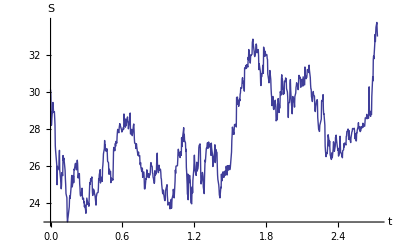

```mathematica
ListPlot[TextPriceData1,PlotJoined->True,AxesLabel->{"t","S"}]
```

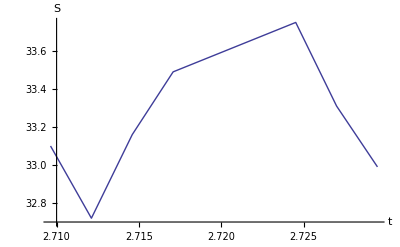

```mathematica
ListPlot[TextPriceData2,PlotJoined->True,AxesLabel->{"t","S"}]
```

```mathematica
InputData=OpenRead["option data0508.txt"]
```

InputStream[option data0508.txt,205]

```mathematica
AllData=Drop[ReadList[InputData,Table[Word,{9}]],-1];
Close[InputData]
```

option data0508.txt

```mathematica
AllData[[-1]]
```

{MSFT,05/08/2013,01/16/2015,40,P,9.5,9.65,10,468}

```mathematica
AllData[[1]]
```

{Ticker,Data,Expiration,Strike,Call/Put,BestBid,BestAsk,Volume,OpenInterest}

```mathematica
F:=Module[{xx,yy,zz},xx=Partition[Append[Prepend[#[[1]]&/@StringPosition[#,"/"],0],StringLength[#]+1],2,1];
yy=ToExpression[Function[y,StringTake[#,y+{1,-1}]]/@xx];zz={#[[3]],#[[1]],#[[2]],16,0,0}&[yy];YearClock[zz]]&
```

```mathematica
AllData2={#[[1]],#[[2]],F[#[[2]]],#[[3]],F[#[[3]]],#[[4]],ToExpression[#[[5]]],ToExpression[#[[6]]],ToExpression[#[[7]]],ToExpression[#[[8]]],ToExpression[#[[9]]],(ToExpression[#[[6]]]+ToExpression[#[[7]]])/2//N}&/@Drop[AllData,1];
```

```mathematica
Take[AllData2,2]
```

{{MSFT,05/08/2013,2.72948,05/9/2013,2.73196,18,C,14.95,15.1,10,916,15.025},{MSFT,05/08/2013,2.72948,05/9/2013,2.73196,19,C,13.95,14.1,40,182,14.025}}

```mathematica
Transpose[%]
```

{{MSFT,MSFT},{05/03/2013,05/03/2013},{2.71708,2.71708},{05/17/2013,05/17/2013},{2.75182,2.75182},{18.00,19.00},{C,C},{14.55,13.95},{16.35,15.7},{10,40},{916,182},{15.45,14.825}}

```mathematica
AllData2[[1]]
```

{MSFT,05/08/2013,2.72948,05/9/2013,2.73196,18,C,14.95,15.1,10,916,15.025}

```mathematica
TimeOfRecord=Union[Transpose[AllData2][[3]]][[1]]
```

2.72948

```mathematica
UnderlyingStockPrice=Select[TextPriceData1,#[[1]]==TimeOfRecord&][[1,2]]
```

32.99

```mathematica
GetAllData["MSFT", OptionType_, Volume_:100, NumberOfExpirations_:3] := 
  Module[{InputData, AllData, F, AllData2, AllCallData, AllCallData2, 
    AllPutData, AllPutData2, x, y, ExpTimes, z}, 
   InputData = InputData = OpenRead[ToFileName[{$TopDirectory, "AddOns", 
         "Applications", "CFMLab", "MarketData"}, 
        "option data.txt"]]; 
    AllData = Drop[ReadList[InputData, Table[Word, {9}]], -1]; 
    Close[InputData]; F := Module[{xx, yy, zz}, 
       xx = Partition[Append[Prepend[(#1[[1]] & ) /@ StringPosition[#1, 
              "/"], 0], StringLength[#1] + 1], 2, 1]; 
        yy = ToExpression[Function[y, StringTake[#1, y + {1, -1}]] /@ 
           xx]; zz = ({#1[[3]] , 
            #1[[1]], #1[[2]], 16, 0, 0} & )[yy]; YearClock[zz]] & ; 
    AllData2 = ({#1[[1]], #1[[2]], F[#1[[2]]], #1[[3]], F[#1[[3]]], 
        ToExpression[#1[[4]]], #1[[5]], ToExpression[#1[[6]]], 
        ToExpression[#1[[7]]], ToExpression[#1[[8]]], 
        ToExpression[#1[[9]]], N[(1/2)*(ToExpression[#1[[6]]] + 
           ToExpression[#1[[7]]])]} & ) /@ Drop[AllData, 1]; 
  AllCallData=Take[AllData2,147];
AllPutData=Take[AllData2,-135];
    AllCallData2 = Transpose[(Transpose[AllCallData][[#1]] & ) /@ 
       {5, 6, -1, -3}]; AllPutData2 = Transpose[
      (Transpose[AllPutData][[#1]] & ) /@ {5, 6, -1, -3}]; 
    x = If[ToString[OptionType] === "Call", AllCallData2, AllPutData2]; 
    y = Select[x, #1[[-1]] >= Volume & ]; 
    ExpTimes = Union[Transpose[y][[1]]]; 
    ExpTimes = Take[ExpTimes, Min[NumberOfExpirations, 
       Length[ExpTimes]]]; z = Function[t, Select[y, #1[[1]] == t & ]] /@ 
      ExpTimes; {{"MSFT", ToString[OptionType], ExpTimes, 
     2.7294833832360093,32.99}, z}]
```

```mathematica
aod=GetAllData["MSFT","Call",300,4]
```

{{MSFT,Call,{2.75182,2.83866,2.90814,2.97762},2.72948,32.99},{{{2.75182,29.,4.25,1417},{2.75182,30.,3.275,1112},{2.75182,31.,2.26,1389},{2.75182,32.,1.79,1308},{2.75182,33.,0.885,7155},{2.75182,34.,0.135,2853},{2.75182,35.,0.03,2132},{2.75182,29.,0.025,387},{2.75182,30.,0.035,359},{2.75182,31.,0.075,451},{2.75182,32.,0.165,1613},{2.75182,33.,0.435,2285}},{{2.83866,29.,4.5,773},{2.83866,30.,3.5,860},{2.83866,31.,2.605,2780},{2.83866,32.,1.79,975},{2.83866,33.,1.13,3932},{2.83866,34.,0.64,1596},{2.83866,35.,0.31,2547},{2.83866,36.,0.135,524}},{{2.90814,29.,4.5,1121},{2.90814,30.,3.6,1618},{2.90814,31.,2.745,1560},{2.90814,32.,2.01,841},{2.90814,33.,1.39,716},{2.90814,34.,0.905,8470},{2.90814,35.,0.545,2675},{2.90814,36.,0.31,427},{2.90814,38.,0.085,328}},{{2.97762,34.,1.065,7511},{2.97762,35.,0.7,448},{2.97762,36.,0.435,329},{2.97762,37.,0.265,1030},{2.97762,38.,0.15,322}}}}

```mathematica
σ=Σ[Select[TextPriceData1,#[[1]]≤YearClock[{2013,5,8,16,0,0}]&]]
```

0.262452

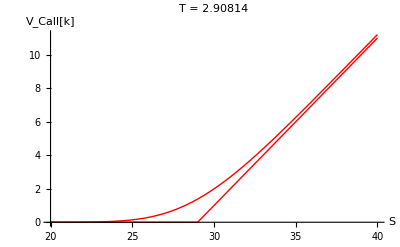

```mathematica
Plot[{Max[S-aod⟦2,3,1,2⟧,0],VC[aod⟦1,4⟧,S,aod⟦2,3,1,1⟧,aod⟦2,3,1,2⟧,.04,σ]},{S,20,40},PlotRange->All,PlotStyle->RGBColor[1,0,0],AxesLabel->{"S","V_Call[k]"},PlotLabel->"T = "<>ToString[aod⟦2,3,1,1⟧]]
```

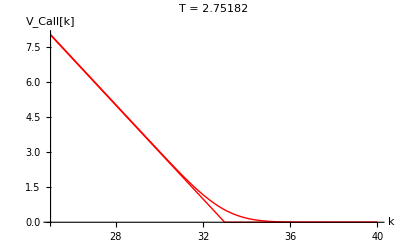

```mathematica
pl=Plot[{Max[aod⟦1,5⟧-k,0],VC[aod⟦1,4⟧,aod⟦1,5⟧,aod⟦2,1,1,1⟧,k,.04,σ]},{k,25,40},PlotRange->All,PlotStyle->RGBColor[1,0,0],AxesLabel->{"k","V_Call[k]"},PlotLabel->"T = "<>ToString[aod⟦2,1,1,1⟧]]
```

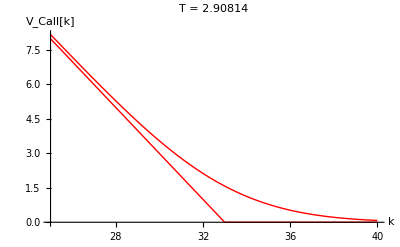

```mathematica
p2=Plot[{Max[aod⟦1,5⟧-k,0],VC[aod⟦1,4⟧,aod⟦1,5⟧,aod⟦2,3,1,1⟧,k,.04,σ]},{k,25,40},PlotRange->All,PlotStyle->RGBColor[1,0,0],AxesLabel->{"k","V_Call[k]"},PlotLabel->"T = "<>ToString[aod⟦2,3,1,1⟧]]
```

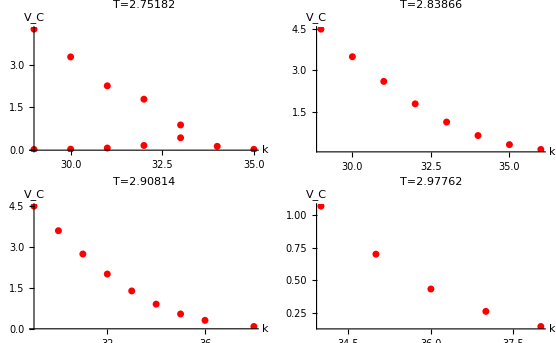

```mathematica
Show[GraphicsGrid[lp=(ListPlot[Transpose[Take[Transpose[#],{2,3}]],AxesLabel->{"k","V_C"},PlotRange->All,PlotStyle->{RGBColor[1,0,0],AbsolutePointSize[5]},DisplayFunction->Identity,PlotLabel->"T="<>ToString[#⟦1,1⟧]]&)/@#&/@Partition[aod[[2]],2]],DisplayFunction->$DisplayFunction]
```

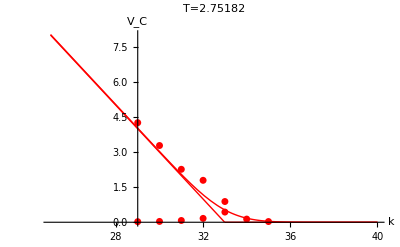

```mathematica
Show[lp⟦1,1⟧,pl,DisplayFunction->$DisplayFunction,PlotRange->All]
```

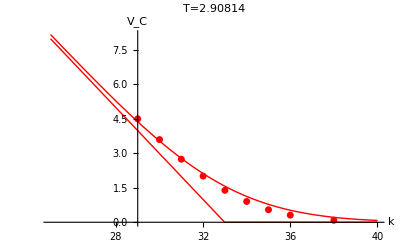

```mathematica
Show[lp⟦2,1⟧,p2,DisplayFunction->$DisplayFunction,PlotRange->All]
```

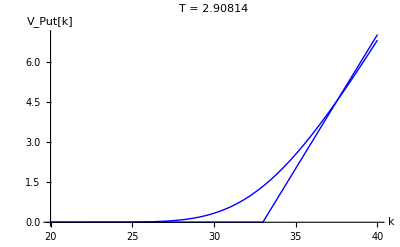

```mathematica
plPut=Plot[{Max[-aod⟦1,5⟧+k,0],VP[aod⟦1,4⟧,aod⟦1,5⟧,aod⟦2,3,1,1⟧,k,.04,σ]},{k,20,40},PlotRange->All,PlotStyle->RGBColor[0,0,1],AxesLabel->{"k","V_Put[k]"},PlotLabel->"T = "<>ToString[aod⟦2,3,1,1⟧]]
```

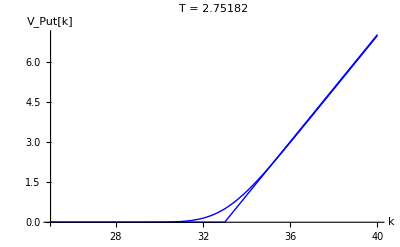

```mathematica
plPut1=Plot[{Max[-aod⟦1,5⟧+k,0],VP[aod⟦1,4⟧,aod⟦1,5⟧,aod⟦2,1,1,1⟧,k,.04,σ]},{k,25,40},PlotRange->All,PlotStyle->RGBColor[0,0,1],AxesLabel->{"k","V_Put[k]"},PlotLabel->"T = "<>ToString[aod⟦2,1,1,1⟧]]
```

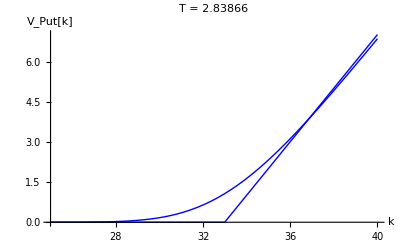

```mathematica
plPut2=Plot[{Max[-aod⟦1,5⟧+k,0],VP[aod⟦1,4⟧,aod⟦1,5⟧,aod⟦2,2,1,1⟧,k,.04,σ]},{k,25,40},PlotRange->All,PlotStyle->RGBColor[0,0,1],AxesLabel->{"k","V_Put[k]"},PlotLabel->"T = "<>ToString[aod⟦2,2,1,1⟧]]
```

```mathematica
aodPut=GetAllData["MSFT","Put",100,4]
```

{{MSFT,Put,{2.75182,2.83866,2.90814,2.97762},2.72948,32.99},{{{2.75182,29.,0.025,387},{2.75182,30.,0.035,359},{2.75182,31.,0.075,451},{2.75182,32.,0.165,1613},{2.75182,33.,0.435,2285},{2.75182,34.,0.99,707},{2.75182,35.,1.815,225}},{{2.83866,24.,0.015,117},{2.83866,26.,0.03,205},{2.83866,27.,0.045,147},{2.83866,28.,0.07,118},{2.83866,29.,0.105,437},{2.83866,30.,0.175,753},{2.83866,31.,0.295,466},{2.83866,32.,0.52,379},{2.83866,33.,0.87,2047},{2.83866,34.,1.38,1134},{2.83866,35.,2.055,1566},{2.83866,36.,2.88,262}},{{2.90814,22.,0.02,210},{2.90814,27.,0.075,130},{2.90814,29.,0.185,426},{2.90814,30.,0.295,146},{2.90814,31.,0.47,267},{2.90814,32.,0.745,824},{2.90814,33.,1.13,600},{2.90814,34.,1.64,616},{2.90814,35.,2.28,269},{2.90814,36.,3.05,110}},{{2.97762,26.,0.105,128},{2.97762,30.,0.45,133},{2.97762,33.,1.405,1167}}}}

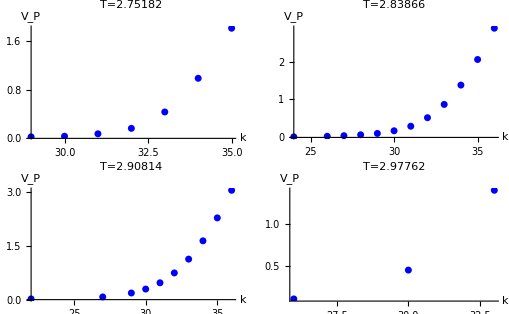

```mathematica
Show[GraphicsGrid[lp2=(ListPlot[Transpose[Take[Transpose[#],{2,3}]],AxesLabel->{"k","V_P"},PlotRange->All,PlotStyle->{RGBColor[0,0,1],AbsolutePointSize[5]},DisplayFunction->Identity,PlotLabel->"T="<>ToString[#⟦1,1⟧]]&)/@#&/@Partition[aodPut[[2]],2]],DisplayFunction->$DisplayFunction]
```

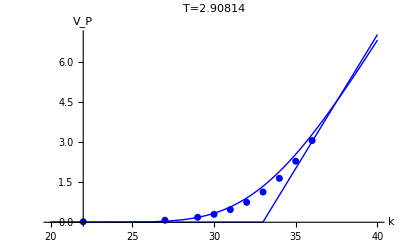

```mathematica
Show[lp2⟦2,1⟧,plPut,DisplayFunction->$DisplayFunction,PlotRange->All]
```

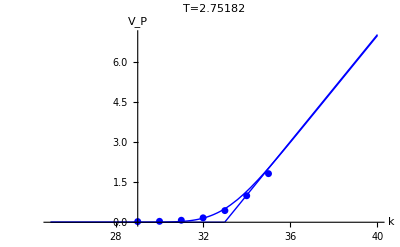

```mathematica
Show[lp2⟦1,1⟧,plPut1,DisplayFunction->$DisplayFunction,PlotRange->All]
```

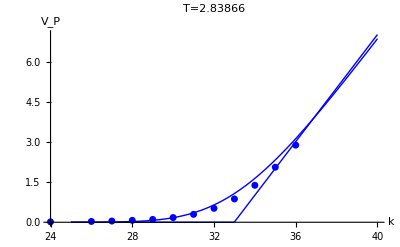

```mathematica
Show[lp2⟦1,2⟧,plPut2,DisplayFunction->$DisplayFunction,PlotRange->All]
```

```mathematica
aod=GetAllData["MSFT","Call",200]
```

{{MSFT,Call,{2.75182,2.83866,2.90814},2.72948,32.99},{{{2.75182,29.,4.25,1417},{2.75182,30.,3.275,1112},{2.75182,31.,2.26,1389},{2.75182,32.,1.79,1308},{2.75182,33.,0.885,7155},{2.75182,34.,0.135,2853},{2.75182,35.,0.03,2132},{2.75182,29.,0.025,387},{2.75182,30.,0.035,359},{2.75182,31.,0.075,451},{2.75182,32.,0.165,1613},{2.75182,33.,0.435,2285}},{{2.83866,29.,4.5,773},{2.83866,30.,3.5,860},{2.83866,31.,2.605,2780},{2.83866,32.,1.79,975},{2.83866,33.,1.13,3932},{2.83866,34.,0.64,1596},{2.83866,35.,0.31,2547},{2.83866,36.,0.135,524}},{{2.90814,29.,4.5,1121},{2.90814,30.,3.6,1618},{2.90814,31.,2.745,1560},{2.90814,32.,2.01,841},{2.90814,33.,1.39,716},{2.90814,34.,0.905,8470},{2.90814,35.,0.545,2675},{2.90814,36.,0.31,427},{2.90814,37.,0.165,214},{2.90814,38.,0.085,328}}}}

```mathematica
aodPut=GetAllData["MSFT","Put",300]
```

{{MSFT,Put,{2.75182,2.83866,2.90814},2.72948,32.99},{{{2.75182,29.,0.025,387},{2.75182,30.,0.035,359},{2.75182,31.,0.075,451},{2.75182,32.,0.165,1613},{2.75182,33.,0.435,2285},{2.75182,34.,0.99,707}},{{2.83866,29.,0.105,437},{2.83866,30.,0.175,753},{2.83866,31.,0.295,466},{2.83866,32.,0.52,379},{2.83866,33.,0.87,2047},{2.83866,34.,1.38,1134},{2.83866,35.,2.055,1566}},{{2.90814,29.,0.185,426},{2.90814,32.,0.745,824},{2.90814,33.,1.13,600},{2.90814,34.,1.64,616}}}}

Part::partw: Part 5 of {{2.97762, 35., 0.7, 448}, {2.97762, 36., 0.435, 329}, {2.97762, 38., 0.15, 322}} does not exist.

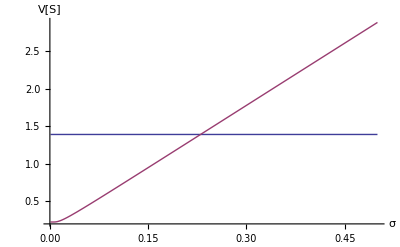

```mathematica
With[{k=5},Plot[{aod⟦2,3,k,3⟧,VC[aod⟦1,4⟧,aod⟦1,5⟧,aod⟦2,3,k,1⟧,aod⟦2,3,k,2⟧,.04,σ]},{σ,.001,.5},PlotRange->All,AxesLabel->{"σ","V[S]"}]]
```

```mathematica
With[{k=5},σ/.FindRoot[aod⟦2,3,k,3⟧==VC[aod⟦1,4⟧,aod⟦1,5⟧,aod⟦2,3,k,1⟧,aod⟦2,3,k,2⟧,.04,σ],{σ,.5}]]
```

0.229954

```mathematica
aod1={{"MSFT","Call",{2.7518155200079404,2.8386627185654496,2.9081404774114574},2.7294833832360093,32.99},{{{2.8386627185654496,29.,4.5,773},{2.8386627185654496,30.,3.5,860},{2.8386627185654496,31.,2.605,2780},{2.8386627185654496,32.,1.79,975},{2.8386627185654496,33.,1.13,3932},{2.8386627185654496,34.,0.64,1596},{2.8386627185654496,35.,0.31,2547},{2.8386627185654496,36.,0.135,524}},{{2.9081404774114574,29.,4.5,1121},{2.9081404774114574,30.,3.5999999999999996,1618},{2.9081404774114574,31.,2.745,1560},{2.9081404774114574,32.,2.01,841},{2.9081404774114574,33.,1.39,716},{2.9081404774114574,34.,0.905,8470},{2.9081404774114574,35.,0.545,2675},{2.9081404774114574,36.,0.31,427},{2.9081404774114574,37.,0.165,214},{2.9081404774114574,38.,0.08499999999999999,328}}}};
```

```mathematica
aod2={{"MSFT","Call",{2.7518155200079404,2.8386627185654496,2.9081404774114574},2.727002034705795,33.31},{{2.7518155200079404,29.,4.25,1417},{2.7518155200079404,30.,3.275,1112},{2.7518155200079404,31.,2.26,1389},{2.7518155200079404,32.,1.79,1308},{2.7518155200079404,33.,0.885,7155},{2.7518155200079404,34.,0.135,2853},{2.7518155200079404,35.,0.03,2132},{2.7518155200079404,29.,0.025,387},{2.7518155200079404,30.,0.035,359},{2.7518155200079404,31.,0.07500000000000001,451},{2.7518155200079404,32.,0.165,1613},{2.7518155200079404,33.,0.435,2285}}};
```

```mathematica
IndividualCallVolatilities[aod_,r_]:=Function[y,(σ/.FindRoot[{aod⟦2,y,#1,3⟧==VC[aod⟦1,4⟧,aod⟦1,5⟧,aod⟦2,y,#1,1⟧,aod⟦2,y,#1,2⟧,r,σ]},{σ,0.5}]&)/@Range[1,Length[aod⟦2,y⟧]]]/@Range[1,Length[aod⟦2⟧]]
```

```mathematica
AllCallVolatilities=IndividualCallVolatilities[aod1,.04]
```

{{0.41984,0.345445,0.301859,0.266159,0.244716,0.230036,0.216654,0.209965},{0.307118,0.279549,0.253925,0.240438,0.229954,0.222501,0.2155,0.211515,0.208544,0.207771}}

```mathematica
IndividualPutVolatilities[aod_,r_]:=Function[y,(σ/.FindRoot[{aod⟦2,y,#1,3⟧==VP[aod⟦1,4⟧,aod⟦1,5⟧,aod⟦2,y,#1,1⟧,aod⟦2,y,#1,2⟧,r,σ]},{σ,.6}]&)/@Range[1,Length[aod⟦2,y⟧]]]/@Range[1,Length[aod⟦2⟧]]
```

```mathematica
AllPutVolatilities=IndividualPutVolatilities[aodPut,.04]
```

{{0.462526,0.383182,0.330119,0.270763,0.226164,0.114803},{0.28636,0.26461,0.243914,0.230117,0.215575,0.200471,0.180926},{0.2639,0.231155,0.223615,0.216467}}

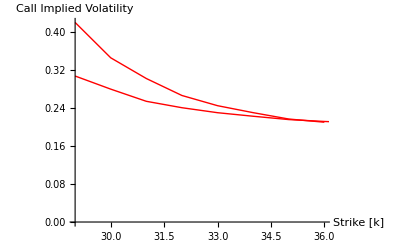

```mathematica
AllCallStrikes=((#1⟦2⟧&)/@#1&)/@aod1⟦2⟧;civ=(ListPlot[#1,DisplayFunction->Identity,PlotStyle->RGBColor[1,0,0],AxesLabel->{"Strike [k]","Call Implied Volatility"},PlotRange->{0,Automatic},PlotJoined->True]&)/@Select[Transpose/@Transpose[{AllCallStrikes,AllCallVolatilities}],Length[#1]≥4&];Show[civ,DisplayFunction->$DisplayFunction]
```

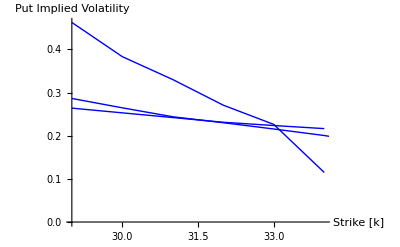

```mathematica
AllPutStrikes=((#1⟦2⟧&)/@#1&)/@aodPut⟦2⟧;
piv=(ListPlot[#1,DisplayFunction->Identity,PlotStyle->RGBColor[0,0,1],AxesLabel->{"Strike [k]","Put Implied Volatility"},PlotRange->{0,Automatic},PlotJoined->True]&)/@Select[Transpose/@Transpose[{AllPutStrikes,AllPutVolatilities}],Length[#1]≥4&];
Show[piv,DisplayFunction->$DisplayFunction]
```

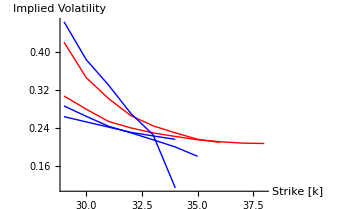

```mathematica
Show[civ,piv,DisplayFunction->$DisplayFunction,AxesLabel->{"Strike [k]","Implied Volatility"},PlotRange->All]
```

```mathematica
Av[List_]:=(Plus@@Flatten[List])/Length[Flatten[List]]
```

```mathematica
{Av[AllCallVolatilities],Av[AllPutVolatilities]}
```

{0.256194,0.255569}

```mathematica
Clear[σ];Subscript[f, p_][σ_]=(Plus@@#1&)[((#1^p&)/@#1&)[Flatten[Function[y,(aod⟦2,y,#1,3⟧-VC[aod⟦1,4⟧,aod⟦1,5⟧,aod⟦2,y,#1,1⟧,aod⟦2,y,#1,2⟧,0.05,σ]&)/@Range[1,Length[aod⟦2,y⟧]]]/@Range[1,Length[aod⟦2⟧]]]]];
```

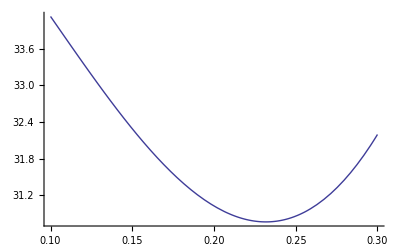

```mathematica
Plot[{Subscript[f, 2][σ]},{σ,.10,.30},PlotRange->All]
```

```mathematica
(FindMinimum[Subscript[f, #1][σ],{σ,.6}]&)/@{2}
```

{{30.7686,{σ→0.231767}}}

```mathematica
ConstantCallVolatility[aod_,r_]:=ConstantCallVolatility[aod,r,4]
ConstantCallVolatility[aod_,r_,p_?EvenQ]:=Module[{f},f=(Plus@@#1&)[((#1^p&)/@#1&)[Flatten[Function[y,(aod⟦2,y,#1,3⟧-VC[aod⟦1,4⟧,aod⟦1,5⟧,aod⟦2,y,#1,1⟧,aod⟦2,y,#1,2⟧,r,σ]&)/@Range[1,Length[aod⟦2,y⟧]]]/@Range[1,Length[aod⟦2⟧]]]]];σ/.FindMinimum[f,{σ,.5}]⟦2⟧]
```

```mathematica
ConstantPutVolatility[aod_,r_]:=ConstantPutVolatility[aod,r,4]
ConstantPutVolatility[aod_,r_,p_?EvenQ]:=Module[{f},f=(Plus@@#1&)[((#1^p&)/@#1&)[Flatten[Function[y,(aod⟦2,y,#1,3⟧-VP[aod⟦1,4⟧,aod⟦1,5⟧,aod⟦2,y,#1,1⟧,aod⟦2,y,#1,2⟧,r,σ]&)/@Range[1,Length[aod⟦2,y⟧]]]/@Range[1,Length[aod⟦2⟧]]]]];σ/.FindMinimum[f,{σ,.5}]⟦2⟧]
```

```mathematica
{ConstantCallVolatility[aod,.05],ConstantPutVolatility[aodPut,.05]}
```

{0.174129,0.222205}